# Frank-Hertz Experiment Josephine Brozny

## Abstract/Introduction

The purpose of the Frank-Hertz experiment is to demonstrate the existence of the Bohr atomic energy levels by observing the energy losses of electrons as they collide with argon atoms. We observed the first excitation potential of Argon and used it to calculate Plank’s constant. We used an oscilloscope in addition to the Frank-Hertz apparatus to plot a current vs grid voltage graph. We were able to take data from the peaks and troughs of the graph in which we calculated 10.9271 as the mean and used to calculate planks constant which we found to be 6.21058×10^-34 J/s. Our calculations closely agree with the accepted value of planks constant; 6.62607×10^-34 J/s.

## Description of Experimental Procedure

We used the Frank-Hertz apparatus and oscilloscope for this experiment. The Frank-Hertz apparatus has an applied filament voltage that allows electrons to emit from a hot cathode. V_G1k is low voltage that is applied from the hot cathode (K( and the grid G2 which accelerated electrons to a desired energy. V_G2P is braking voltage which is applied between anode (P) and grid (G2)

To begin the procedure, we began setting up the oscilloscope to record the plot of current vs voltage. We did not have to change the settings on the oscilloscope because it was already correct when we arrived to our lab station, although we did change the volt/div knob which reflects the channel 1.00 V/div and the mV/div knob to reflect the channel 50.0 mV/div. Afterwards we pressed the “PERSIST” button which then set to “infinity” which allowed our graph to stay on the screen until we decided to clear it, this made it a lot easier to take data. Then with the Frank-Hertz apparatus we adjusted each knob V_G2P, V_F, V_G1K, and V_G2K to the number listed on the top of the apparatus. We only adjusted the V_G2K knob continuously during this experiment. Once everything was aligned we began taking data. We also observed that the scaling on the oscilloscope was correct and didn’t need altering. We turned the V_G2K knob between 0-90 Volts in order to see the graph on the oscilloscope.

## Results

### Part I: Results

From the data we measured, we were able to determine the mean of the excitation values which is 10.9. The minimum (troughs) represent the number of collisions that the excited electrons reached. The maximum (peaks) represent the state of the electrons having enough energy to be excited. We were able to determine Plank’s constant from our data and measurements in which we came very close to the respected value of 6.626x10^-34 J*Hz^-1 whereas we calculated 6.216x10^-34J*Hz^-1. This is within our calculated uncertainty range of (+/-) 0.4 which we determined by utilizing uncertainty propagation and and therefore are in agreement with he accepted value of planks constant. As part of our data calculations we displayed a histogram graph which shows a normal standard deviation range which solidifies that the errors in our experiment are only small, random errors.

#### Data input

```mathematica
excitationvalues={10.2,10.4,10.7,11.2,11.6,11.7,10.0,10.5,10.5,11.2,11.2,11.9,10.1,10.2,10.4,11.2,11.6,11.9,10.0,10.2,10.9,11.2,11.4,11.7,10.2,10.1,10.9,10.7,11.8,11.7,10.3,10.4,10.8,11.1,11.2,11.8,10.4,9.9,10.6,11.1,11.6,12.0,10.4,10.7,10.6,11.1,11.6,11.6}
lambda=1.067*10^(-7) 
e=1.602*10^(-19)
c=3*10^8
```

{10.2,10.4,10.7,11.2,11.6,11.7,10.,10.5,10.5,11.2,11.2,11.9,10.1,10.2,10.4,11.2,11.6,11.9,10.,10.2,10.9,11.2,11.4,11.7,10.2,10.1,10.9,10.7,11.8,11.7,10.3,10.4,10.8,11.1,11.2,11.8,10.4,9.9,10.6,11.1,11.6,12.,10.4,10.7,10.6,11.1,11.6,11.6}

1.067×10^-7

1.602×10^-19

300000000

{10.1,10.2,9.8,11,11.3}

{0.2,0.3,0.5,0.4,0.1,-1.7,0.5,0.,0.7,0.,0.7,-1.8,0.1,0.2,0.8,0.4,0.3,-1.9,0.2,0.7,0.3,0.2,0.3,-1.5,-0.1,0.8,-0.2,1.1,-0.1,-1.4,0.1,0.4,0.3,0.1,0.6,-1.4,-0.5,0.7,0.5,0.5,0.4,-1.6,0.3,-0.1,0.5,0.5,0.}

#### Calculations:

```mathematica
Mean[excitationvalues]
StandardDeviation[excitationvalues]
planksconstant=((e)(v)(lambda))/(c)
```

10.9271

0.62185

6.21058×10^-34

```mathematica
0.6218502191327594
```

0.62185

Histogram::ldata: excitationvalues is not a valid dataset or list of datasets.

Histogram[excitationvalues]

Plot::plln: Limiting value xmin in {x,xmin,xmax} is not a machine-sized real number.

Plot[√(2 pi sigma) Exp[-(x-mean)^2/(2 sigma^2)],{x,xmin,xmax},PlotRange→All]

Show::gcomb: Could not combine the graphics objects in Show[Histogram[excitationvalues],Plot[√(2 pi sigma) Exp[-Plus[«2»]^2/(2 Power[«2»])],{x,xmin,xmax},PlotRange→All]].

Show[Histogram[excitationvalues],Plot[√(2 pi sigma) Exp[-(x-mean)^2/(2 sigma^2)],{x,xmin,xmax},PlotRange→All]]

#### Part 2: Graph

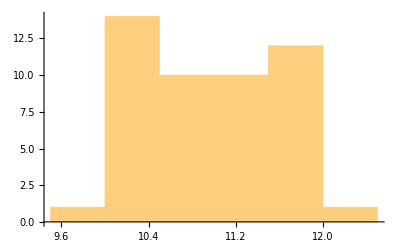

Plot::plln: Limiting value xmin in {x,xmin,xmax} is not a machine-sized real number.

Plot[√(2 pi sigma) Exp[-(x-mean)^2/(2 sigma^2)],{x,xmin,xmax},PlotRange→All]

Show::gcomb: Could not combine the graphics objects in Show[,Plot[√(2 pi sigma) Exp[-Plus[«2»]^2/(2 Power[«2»])],{x,xmin,xmax},PlotRange→All]].

Show[-Graphics-,Plot[√(2 pi sigma) Exp[-(x-mean)^2/(2 sigma^2)],{x,xmin,xmax},PlotRange→All]]

```mathematica
hist=Histogram[excitationvalues]
prob=Plot[(2*pi*sigma)^(1/2)*Exp[-(x-mean)^2/(2*sigma^2)],
	{x,xmin,xmax},PlotRange->All]
Show[hist,prob]
```

## Discussion

Our calculated value for Plank’s constant agrees with the accepted value of Plank’s constant. Our calculated value was 6.1266x10^-34 J*H^-1 with an uncertainty of (+/-) o.4 and the accepted value is 6.626x10^-34 J*Hz^-1. We used uncertainty propagation in order to determine the uncertainty values we measures for the maximum’s (peaks) and minimum’s (troughs) which came out to be (+/-) 0.2. We incorporated this uncertainty because when observing the graph it looked as if you could move the knob (+/-) 0.2 in each direction and still appear to be directly lined up with the max or min. We were able to determine 0.4 from adding and subtracting these measurements and uncertainty propagation gave us 0.4 uncertainty. The most prominent reason for systematic error would be the change in data-taker. Me and my partner switched every trial and we may have read the graph differently or moved the knob differently. We also could have contributed to a human error of simply not observing correctly and/or not lining up on the max or min individually, which when we switched trials, could have created a larger systematic error because our observations differed.

## Conclusion

In this lab we were able to calculate Plank’s constant by using the Frank-Hertz apparatus and an oscilloscope by measuring the maximum and minimum values of the current vs voltage graph (excitation values) and calculating the mean and standard deviation. We were able to calculate Plank’s constant to be 6.2166x10^-34 (+/-) 0.4 J*Hz^-1 which is in agreement with the accepted value: 6.626x10^-34 J*Hz^-1. By doing so we gained an understanding of the energy levels of electrons of Argon and the existence of Bohr atomic energy levels.